# Load Files

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[],"DoubleBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis3.txt"}]];


LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_DB,Infinity];
```

# Generate Phase-Space Point

{d→978475355,mTsq→326224558,s15→1437707243,s23→83414795,s45→538177826}

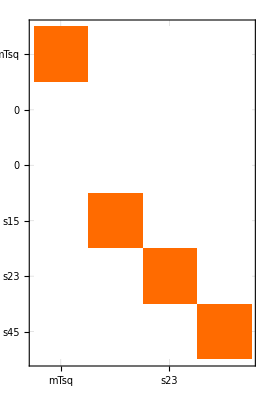

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
PureIntegralN=Expand[PureIntegrals/.tPoint/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P];
diffOp=getDifferentialOperator[tPoint];
epsrepl={(ep->(4-d)/2)/.tPoint};
checkDifferentialOperator[tPoint,diffOp]
```

# Compute Basis Change Matrix

0

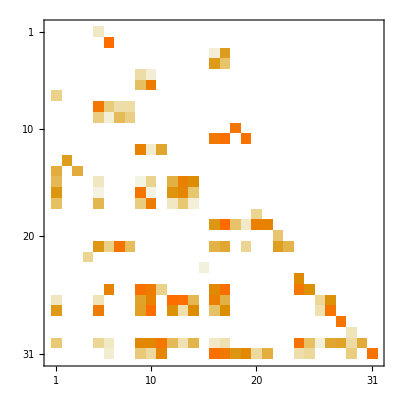

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/DB/numerics_2147483647_0.m"}]];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
Basis=Cases[PureIntegralN2,_TTH,Infinity]//DeleteDuplicates;
NullInts=Thread[Rule[Complement[Basis,LaportaBasis],0]]//EchoFunction[Length];
PureIntegralN2=PureIntegralN2/.NullInts;
BasisChangMat=Table[CoefficientArrays[Expand[PureIntegralN2/.epsrepl,Modulus->$P][[pos]],LaportaBasis],{pos,1,31}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat//MatrixPlot
```

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[Delete[{1,2,3,4,5},var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],ProgressIndicator[(var-1)*31+intpos,{1,31*6}]];
```

## Extra Step If Redu List does not exits yet

```mathematica
ToReduce=Cases[diffInts,_DB,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

271

```mathematica
ToReduce2=Cases[PureIntegralN,_DB,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

32

```mathematica
WriteJobFile[{"UReduList","ReduList"}]
```

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_DB,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,LaportaBasis];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

38

# Compute DE Matrices

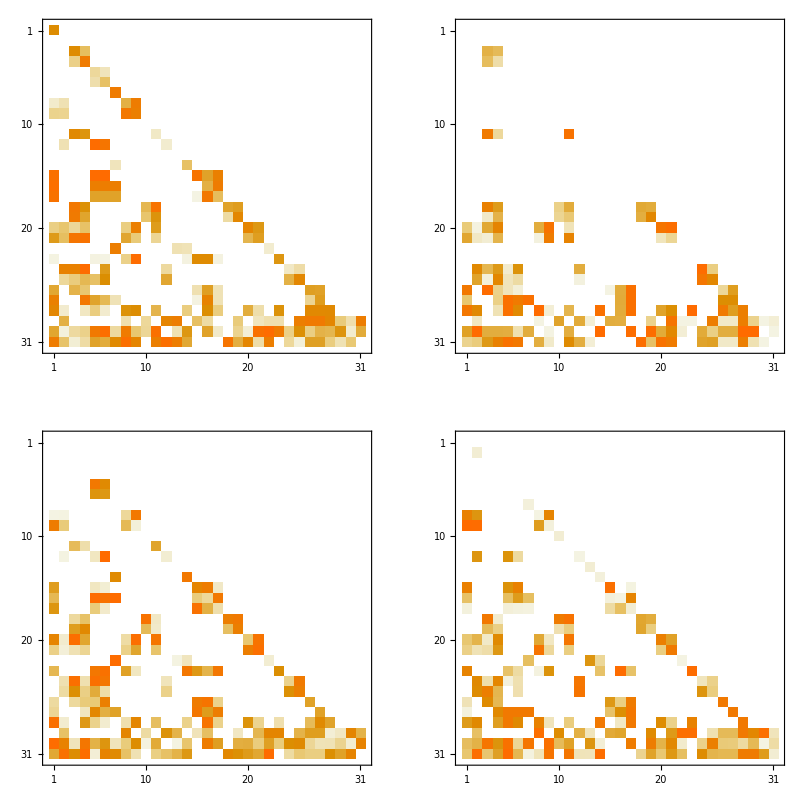

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],LaportaBasis]/.{0}->{0,ConstantArray[0,31]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[LaportaBasis]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[4]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot2},{Mplot3,Mplot4}}]
```